## Problem Set 08

## Check for local bifurcations

### Check for saddle-node, transcritical, or pitchfork bifurcations (look at the determinant)

```mathematica
f[x_,y_] ={ y + b x, -x + b y - x^2 y}
fp = Solve[f[x,y]==0,{x,y}]
jacobian = Grad[f[x,y],{x,y}];
tracevals = Tr[jacobian]/.fp;
detvals = Det[jacobian]/.fp;
Table[Solve[detvals[[k]]==0,μ],{k,1,3}] (* Use "Table" to process each fixed point separately. *)
(* None of the fixed points in this system have Determinant zero at any real parameter value, so no saddle-node/transcritical/pitchfork.*)
```

{b x+y,-x+b y-x^2 y}

{{x→0,y→0},{x→-(√(1+b^2))/(√b),y→√b √(1+b^2)},{x→(√(1+b^2))/(√b),y→-√b √(1+b^2)}}

{{},{},{}}

### Check for Hopf bifurcations (look at the trace and determinant)

```mathematica
possiblehopf = Table[Solve[tracevals[[k]]==0,b],{k,1,3}] 
(* Use "Table" to process each fixed point separately. *)
(* Each of the fixed points has trace = 0 for at least one parameter value.*)
Table[detvals[[k]]/.possiblehopf[[k]],{k,1,3}]
(* Check the value of the determinant for each fixed point at the parameter values where the trace is zero *)
```

{{{b→0}},{{b→-1},{b→1}},{{b→-1},{b→1}}}

{{1},{-4,-4},{-4,-4}}

## Attempt to classify a Hopf bifurcation using phase portraits and trajectories

The Hopf bifurcation in the example above occurs at (0, 0) when μ = 0 (trace = 0 and det > 0)

```mathematica
fp = {x->0,y->0};
determ = Det[jacobian]/.fp
trace = Tr[jacobian]/.fp
(* (0,0) is stable for μ<0 and unstable for μ>0 *)
```

1+b^2

2 b

### Is the bifurcation subcritical or supercritical?

If the bifurcation is subcritical, an unstable limit cycle is born at the bifurcation point around the stable fixed point.
No new limit cycle is created around the unstable fixed point.

If the bifurcation is supercritical, a stable limit cycle is born at the bifurcation point around the unstable fixed point.
No new limit cycle is created around the stable fixed point.

We will create trajectories to look for these limit cycles.

- Stay close to the bifurcation value so that the new limit cycle remains small.
- Use initial conditions close to the fixed point.
- Use backward time integration on the side with the stable fixed point so that an unstable limit cycle would be stabilized.
- Use forward time integration on the side with the unstable fixed point so that a stable limit cycle would be stable.


You should observe:
- One of the trajectories saturates at a small limit cycle (that is the side with the new limit cycle)
- The other trajectory may saturate at a larger limit cycle or may escape to infinity.

There may be other limit cycles in the system. Our goal is to isolate the newly created cycle, whose radius approaches zero at the bifurcation point. For this reason, keep both the parameter value and the initial condition close to the bifurcation point.

Flow is slow very close to the fixed point and very close to the bifurcation point, so we choose to be close, but not extremely close.

#### Explore the behavior of trajectories near the bifurcation and near the fixed point

On the side with the stable fixed point (b = bcritical + bstable*bdelta) create a backward time trajectory to look for an unstable limit cycle that is stabilized in backward time.

On the side with the unstable fixed point (b = bcritical - bstable*bdelta) create a forward time trajectory to look for a stable limit cycle that is stable in forward time.

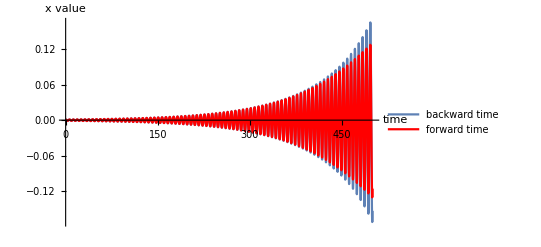

```mathematica
forwards[x_,y_]=f[x,y];
backwards[x_,y_]=-f[x,y];
bcritical = 0;
bdelta=0.01;
bstable=-1;  (* stable is below bcritical is use 
-1 for the stable direction for this system *)
xyIC = {0.001,0};
tmax = 500;
bbk=bcritical+bstable*bdelta;
bfwd=bcritical-bstable*bdelta;
solbk = NDSolve[{{x'[t],y'[t]}==(backwards[x[t],y[t]]/.b->bbk),x[0]==xyIC[[1]],y[0]==xyIC[[2]]},{x,y},{t,0,tmax}];
solfwd= NDSolve[{{x'[t],y'[t]}==(forwards[x[t],y[t]]/.b->bfwd),x[0]==xyIC[[1]],y[0]==xyIC[[2]]},{x,y},{t,0,tmax}];
pbck=Plot[{(x[t]/.solbk)},{t,0,tmax},PlotRange->All,AxesLabel->{"time","x value"},AxesStyle->Directive[FontSize,12],PlotLegends->{"backward time"}];
pfwd=Plot[{(x[t]/.solfwd)},{t,0,tmax},PlotRange->All,PlotStyle->Red,PlotLegends->{"forward time"}];
Show[pbck,pfwd]
```

Integrate longer in time to observe saturation.
Only plot to an end time for which the integration worked (solutions may diverge to infinity).

NDSolve::ndsz: At t == 565.295, step size is effectively zero; singularity or stiff system suspected.

565.295

800.

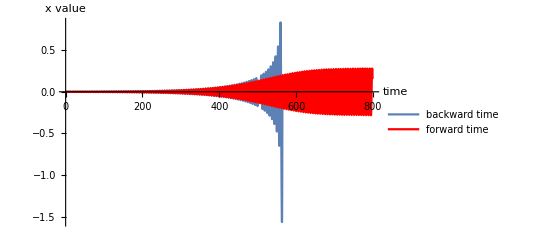

```mathematica
tmax2 = 800;

solbk2 = NDSolve[{{x'[t],y'[t]}==(backwards[x[t],y[t]]/.b->bbk),x[0]==xyIC[[1]],y[0]==xyIC[[2]]},{x,y},{t,0,tmax2}];
solfwd2= NDSolve[{{x'[t],y'[t]}==(forwards[x[t],y[t]]/.b->bfwd),x[0]==xyIC[[1]],y[0]==xyIC[[2]]},{x,y},{t,0,tmax2}];
(* we run into an integration error because one of the trajectories is diverging to infinity *)
tmaxActualbk = (x/.solbk2[[1]])["Domain"][[1,2]]
pbck2=Plot[{(x[t]/.solbk2)},{t,0,tmaxActualbk-1},PlotRange->All,AxesLabel->{"time","x value"},AxesStyle->Directive[FontSize,12],PlotLegends->{"backward time"}];
tmaxActualfw = (x/.solfwd2[[1]])["Domain"][[1,2]]
pfwd2=Plot[{(x[t]/.solfwd2)},{t,0,tmaxActualfw-1},PlotRange->All,PlotStyle->Red,PlotLegends->{"forward time"}];
Show[pbck2,pfwd2]
```

#### We see that forward time saturates to a stable limit cycle, so this is a supercritical Hopf (if backward time had saturated to a nearby limit cycle it would be a subcritical Hopf)

## Create a phase portrait on either side of the bifurcation

#### Start with streamplot and fixed point(s)

```mathematica
vectorfield[x,y]/.b->bbk
```

{-0.01 x+y,-x-0.01 y-x^2 y}

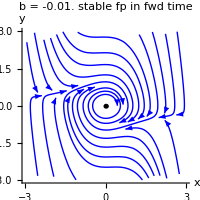

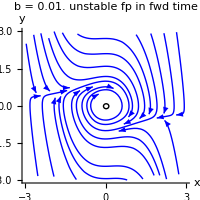

```mathematica
(* For supercritical,use forward_eq
   For subcritical,use backward_eq*)
vectorfield[x_,y_]=forwards[x,y];
(*vectorfield_eq=backward_eq *)

(* fixed point location doesn't depend on b for this portrait *)
fpstable = Graphics[Disk[{0,0},0.1]];
fpunstable = Graphics[Circle[{0,0},0.1]];

p1a = StreamPlot[vectorfield[x,y]/.b->bbk,{x,-3,3},{y,-3,3},StreamPoints->20,Frame->None,Axes->True,AxesLabel->{x,y},ImageSize->{200,200},StreamScale->Large,StreamStyle->{Blue,"Line"},PlotLabel->StringForm["b = ``. stable fp in fwd time",bbk]];
p1b=Normal[p1a]/. Line[x_]:>{Arrowheads[{{0.06,0.5}}],Arrow[x]};
p1 = Show[p1b,fpstable]

p2a = StreamPlot[vectorfield[x,y]/.b->bfwd,{x,-3,3},{y,-3,3},StreamPoints->20,Frame->None,Axes->True,AxesLabel->{x,y},ImageSize->{200,200},StreamScale->Large,StreamStyle->{Blue,"Line"},PlotLabel->StringForm["b = ``. unstable fp in fwd time",bfwd]];
p2b=Normal[p2a]/. Line[x_]:>{Arrowheads[{{0.06,0.5}}],Arrow[x]};
p2 = Show[p2b,fpunstable]
```

#### Add a trajectory that starts a little further out

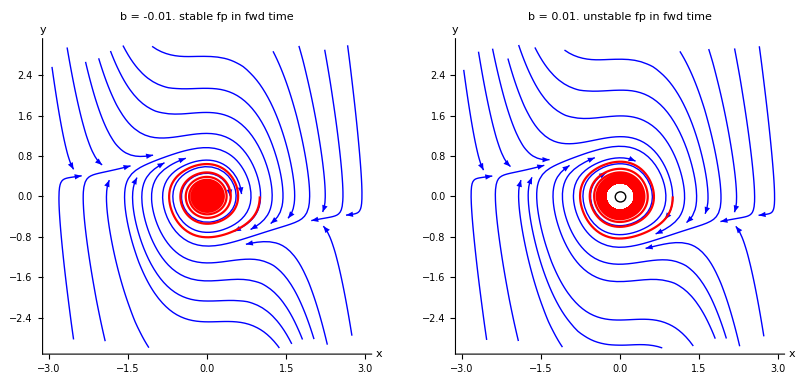

```mathematica
xy0 = {1,0};
tmax3 = 1000;
sol3a = NDSolve[{{x'[t],y'[t]}==(vectorfield[x[t],y[t]]/.b->bbk),x[0]==xy0[[1]],y[0]==xy0[[2]]},{x,y},{t,0,tmax3}];
sol3b= NDSolve[{{x'[t],y'[t]}==(vectorfield[x[t],y[t]]/.b->bfwd),x[0]==xy0[[1]],y[0]==xy0[[2]]},{x,y},{t,0,tmax3}];
p3a=ParametricPlot[{x[t],y[t]}/.sol3a,{t,0,tmax3},PlotRange->All,AxesLabel->{"time","x value"},AxesStyle->Directive[FontSize,12],PlotStyle->Red,PlotPoints->200];
p3b=ParametricPlot[{x[t],y[t]}/.sol3b,{t,0,tmax3},PlotRange->All,AxesLabel->{"time","x value"},AxesStyle->Directive[FontSize,12],PlotStyle->Red,PlotPoints->200];
GraphicsGrid[{{Show[p1,p3a,ImageSize->Medium],Show[p2,p3b,ImageSize->Medium]}}]
```

#### We see spiraling into the fixed point on the stable side and spiraling into a limit cycle on the unstable side. These were done in forward time and the limit cycle is around the unstable fixed point. This is typical for a supercritical Hopf.

## Poincaré map to check for the limit cycle.

### Choose a vertical line segment above the fixed point

We start trajectories on a line segment above the fixed point and look for when they return to that line segment.

Note: this is a slightly different example system than above, with fixed point at (1,0).

{m (-1+x)+y,1-x+m y-(-1+x)^2 y}

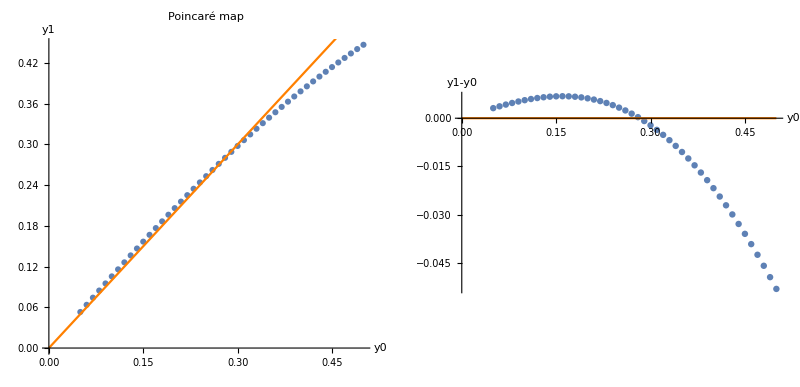

```mathematica
f[x_,y_]={y+m*(x-1),-(x-1)+m*y-(x-1)^2*y}
g[x_,y_]=f[x,y]/.m->0.01; (* m = 0.01 is a parameter value with a limit cycle*)
fixedpointlocation={1,0};  (* set the fixed point *)
maxtime = 50;  (* integration needs to be long enough to return to the line segment *)
ymin = 0.05;
ymax = 0.5;
(* the radius of the limit cycle needs to be between ymin and ymax for us to see it *)
ystep = 0.01;

ystop={};
plotlist={};
startval=fixedpointlocation[[2]]+ymin;
stopval=fixedpointlocation[[2]]+ymax;
ystart=Table[val,{val,startval,stopval,ystep}];  (*ystart is a list of initial y-values*)

For[ii=1,ii<=Length[ystart],ii=ii+1,y0=ystart[[ii]];(*set the initial y value with the ii-th element of ystart*)solveforward=NDSolve[{x'[t]==g[x[t],y[t]][[1]],y'[t]==g[x[t],y[t]][[2]],x[0]==fixedpointlocation[[1]],y[0]==y0,WhenEvent[x[t]==fixedpointlocation[[1]]&&y[t]>fixedpointlocation[[2]],"StopIntegration"]},{x,y},{t,maxtime},Method->"BDF"];(*stop the integration when we return to the positive y-axis*)

solval=x/. solveforward[[1]];(*pull out the x(t) solution*)
{beginb,endb}=solval["Domain"][[1]];(*find the time bounds associated with it*)

AppendTo[ystop,y[endb]/. solveforward[[1]]]; (*evaluate y at the stopping time*)]

p1=Plot[x,{x,0,stopval},PlotStyle->Orange];
p2=ListPlot[Transpose[{ystart,ystop}],PlotMarkers->Automatic,AxesLabel->{"y0","y1"},PlotLabel->"Poincaré map",AspectRatio->1];
poincare = Show[p2,p1,ImageSize->Medium];

y0y1diff = ListPlot[Transpose[{ystart,ystop-ystart}],AxesLabel->{"y0","y1-y0"},LabelStyle->Medium];
p0 = Plot[0,{x,0,0.5},PlotStyle->Orange];
diffmap = Show[y0y1diff,p0,ImageSize->Medium];

GraphicsGrid[{{poincare,diffmap}}]
(*The Poincare map data is so close to the y1 =y0 line that it is hard to tell! So plot y1-y0.*)
```

### Adjust the line segment to focus on the fixed point

{y+x μ,-x-x^2 y+y μ}

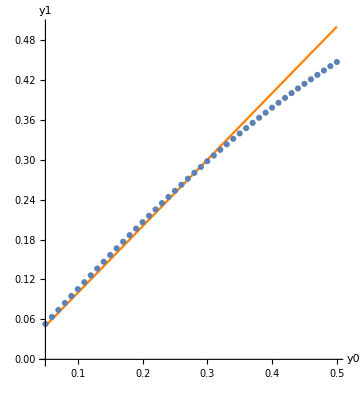

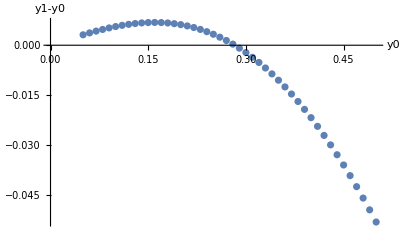

```mathematica
f[x_,y_]={y+μ x,-x+μ y-x^2 y}
g[x_,y_]=f[x,y]/.μ->0.01;
fpxval=0;
fpyval=0;
ystop={};
plotlist={};
(*the table of values for the poincare map needs to span the suspected limit cycle.*)
startval=fpyval+0.05;
stopval=fpyval+0.5;
ystart=Table[val,{val,startval,stopval,0.01}];  (*ystart is a list of initial y-values*)
For[ii=1,ii<=Length[ystart],ii=ii+1,y0=ystart[[ii]];(*set the initial y value with the ii-th element of ystart*)solveforward=NDSolve[{x'[t]==g[x[t],y[t]][[1]],y'[t]==g[x[t],y[t]][[2]],x[0]==fpxval,y[0]==y0,WhenEvent[x[t]==fpxval&&y[t]>fpyval,"StopIntegration"]},{x,y},{t,40},Method->"BDF"];(*stop the integration when we return to the positive y-axis*)
solval=x/. solveforward[[1]];(*pull out the x(t) solution*)
{beginb,endb}=solval["Domain"][[1]];(*find the time bounds associated with it*)
AppendTo[ystop,y[endb]/. solveforward[[1]]]; (*evaluate y at the stopping time*)]
p1=Plot[x,{x,startval,stopval},PlotStyle->Orange,AspectRatio->Automatic,AxesLabel->{"y0","y1"},LabelStyle->Medium];
p2=ListPlot[Transpose[{ystart,ystop}],PlotMarkers->Automatic];
Show[p1,p2]
(*This is so close to the y1=y0 line that it is hard to tell! So plot y1-y0.*)
ListPlot[Transpose[{ystart,ystop-ystart}],AxesLabel->{"y0","y1-y0"},LabelStyle->Medium]
```

From the Poincaré map, I see that there is a limit cycle.  The slope of the map curve is positive, and less than 1, at the fixed point so this is a stable limit cycle.

#### It would be nice to check that the limit cycle size scales reasonably (radius should grow as sqrt(m))

If our Hopf appears to be subcritical then do this using the backwards time system (so that the limit cycle is stabilized).  If supercritical then use the forward time system.  We will not do that work here.

## Extra Example: Restrict the domain in solve for an angular variable

```mathematica
fp = Solve[{Cos[x]==0,0≤ x,x<2Pi},x]
```

{{x→π/2},{x→(3 π)/2}}